```mathematica
raw=Import["C:\\Users\\willc\\OneDrive\\Desktop\\Cycles\\research_data\\output\\menstrual.txt"];
```

```mathematica
sets=StringSplit[raw, "\n\n"];
```

```mathematica
datasets=<||>;
```

```mathematica
Table[
Module[
{rows=StringSplit[s,"\n"]},
datasets[rows[[1]]]=ToExpression/@(StringSplit[#," "]&/@rows[[2;;]])
],{s,sets}];
```

```mathematica
errorsDate=Table[(#[[3]]-#[[1]])/(#[[1]])*100&/@x,{x,datasets}];
```

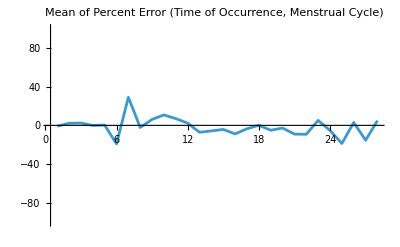

```mathematica
ListLinePlot[Table[Mean[#[[i]]&/@Select[errorsIntensities,Length[#]>=i&]],{i,1,28}],PlotRange->{All,{-100,100}},PlotLabel->"Mean of Percent Error\n(Time of Occurrence, Menstrual Cycle)"]
```

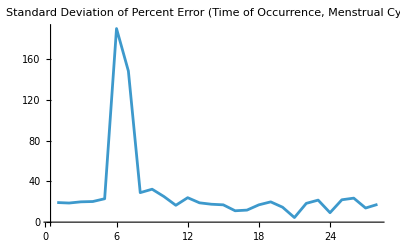

```mathematica
ListLinePlot[Table[StandardDeviation[#[[i]]&/@Select[errorsIntensities,Length[#]>=i&]],{i,1,28}],PlotLabel->"Standard Deviation of Percent Error\n(Time of Occurrence, Menstrual Cycle)",PlotRange->All]
```

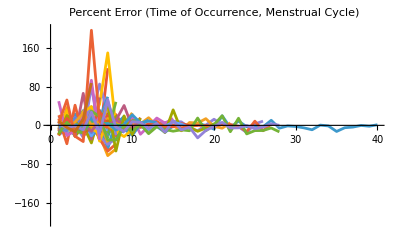

```mathematica
ListLinePlot[errorsDate, PlotRange->{{0,40},{-200,200}},PlotLabel->"Percent Error (Time of Occurrence, Menstrual Cycle)"]
```

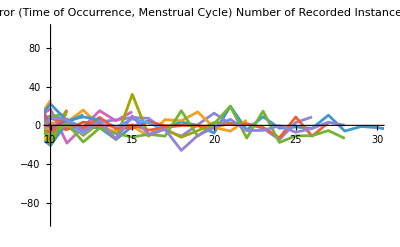

```mathematica
ListLinePlot[errorsDate, PlotRange->{{10,30},{-100,100}},PlotLabel->"Percent Error (Time of Occurrence, Menstrual Cycle)\nNumber of Recorded Instances from 10 to 30"]
```

```mathematica
errorsIntensities=Table[(#[[4]]-#[[2]])/(#[[2]])*100&/@x,{x,datasets}];
```

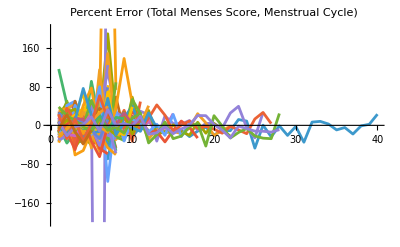

```mathematica
ListLinePlot[errorsIntensities, PlotRange->{{0,40},{-200,200}},PlotLabel->"Percent Error (Total Menses Score, Menstrual Cycle)"]
```

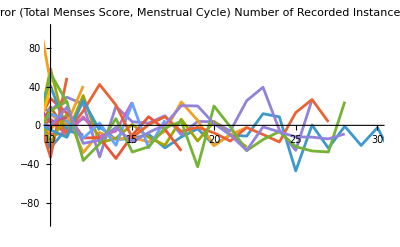

```mathematica
ListLinePlot[errorsIntensities, PlotRange->{{10,30},{-100,100}},PlotLabel->"Percent Error (Total Menses Score, Menstrual Cycle)\nNumber of Recorded Instances from 10 to 30"]
```

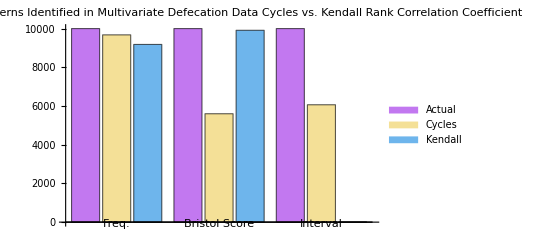

```mathematica
BarChart[{{10000,9675,9180},{10000,5600,9911},{10000,6064,0}},ChartLabels->{{"Freq.","Bristol Score","Interval"},None},ChartLegends->{"Actual","Cycles","Kendall"},ChartStyle->"Pastel",PlotLabel->"Number of Patterns Identified in Multivariate Defecation Data\nCycles vs. Kendall Rank Correlation Coefficient"]
```

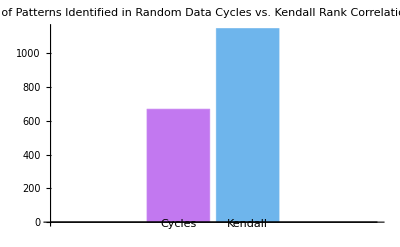

```mathematica
BarChart[{669,1147},ChartLabels->{"Cycles","Kendall"},ChartStyle->"Pastel",PlotLabel->"Number of Patterns Identified in Random Data\nCycles vs. Kendall Rank Correlation Coefficient"]
```